853

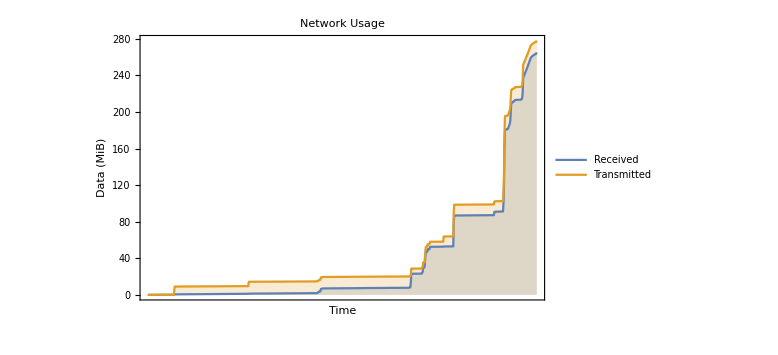

```mathematica
intItpr=Internal`StringToMInteger[#]&;
range={DateObject[{2023,6,14,0,0},"Minute","Gregorian",8.],Now};
range=ToString/@UnixTime/@range;
text=Import["http://bczhc.ml/server-network-log/get?time="<>range[[1]]<>".."<>range[[2]]<>"&bzip3=false","Text"];
handleLine[line_]:=intItpr@#&/@StringSplit[line];
data=handleLine@#&/@StringSplit[text,"\n"]//Parallelize;
data=({FromUnixTime@#[[1]],#[[2]],#[[3]]})&/@data;//Parallelize
firstRx=data[[1]][[2]];
firstTx=data[[1]][[3]];
data=({#[[1]],Quantity[#[[2]]-firstRx,"MiB"],Quantity[#[[3]]-firstTx,"MiB"]})&/@data//Parallelize;
Length@data
(*data=data[[1;;-1;;IntegerPart[Length@data/1000]]];*)
rxData={#[[1]],#[[2]]/1048576}&/@data;
txData={#[[1]],#[[3]]/1048576}&/@data;
dates=#[[1]]&/@data;
length=Length@data;
DateListPlot[{rxData,txData},
ImageSize->Large,
PlotLegends->{"Received","Transmitted"},
FrameLabel->{"Time","Data (MiB)"},
PlotLabel->"Network Usage",
Filling->Bottom,
DateTicksFormat->{"MonthNameShort"," ","Day"},
FrameTicks->{Automatic,{dates[[1;;-1;;IntegerPart[length/7]]],None}}
]
```